```mathematica
rawData = Partition[ReadList["C:/Unity/SyntheticGS/Assets/HDRI/Histogram.dat", "Number"], 100];
Manipulate[BarChart[rawData[[a]]], {a, 1, 10, 1}]
```

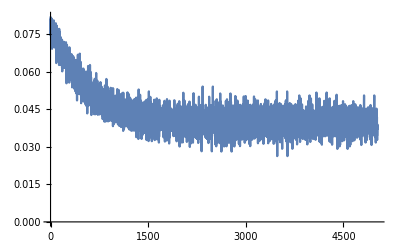

```mathematica
lossData = Partition[ReadList["C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat", "Number"], 2];
ListLinePlot[lossData, PlotRange->All]
```

Options::strmn: Requested stream InputStream[C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat,81] does not match existing stream {System`Private`StringTurnedIntoStream[0 3.495140 1 1.477743 2 1.183390 3 0.937683 4 0.663062 5 0.483333 6 0.459410 7 0.446719 8 0.449122 9 0.419077 10 0.408901 11 0.3...91 0.064774 15692 0.058413 15693 0.068857 15694 0.080157 15695 0.072442 15696 0.062656 15697 0.081720 15698 0.072080 15699 0.072654 ],{False,String,False},-Medium-} with the same stream number.

InputStream[…]

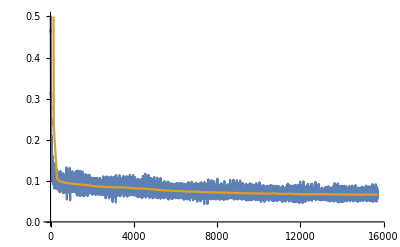

```mathematica
filePath = "C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat";
miniBatchStr = ReadLine[filePath];
epochStr = ReadLine[filePath];
Close[filePath];
StringToStream[miniBatchStr]
epochLoss = Partition[ReadList[StringToStream[epochStr], "Number"], 2];
miniBatchLoss= Partition[ReadList[StringToStream[miniBatchStr], "Number"], 2];
ListLinePlot[{miniBatchLoss, epochLoss}, PlotRange->{All, {0, 0.5}}]
```

Options::strmn: Requested stream InputStream[C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat,126] does not match existing stream {System`Private`StringTurnedIntoStream[0 0.041505 1 0.041629 2 0.044985 3 0.049098 4 0.038630 5 0.043130 6 0.043522 7 0.040460 8 0.040242 9 0.043162 10 0.041689 11 0.0...91 0.034848 31392 0.036033 31393 0.036729 31394 0.029992 31395 0.036983 31396 0.036893 31397 0.034417 31398 0.039004 31399 0.047237 ],{False,String,False},-Medium-} with the same stream number.

InputStream[…]

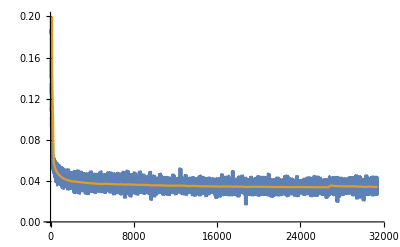

```mathematica
filePath = "C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat";
miniBatchStr = ReadLine[filePath];
epochStr = ReadLine[filePath];
Close[filePath];
StringToStream[miniBatchStr]
epochLoss = Partition[ReadList[StringToStream[epochStr], "Number"], 2];
miniBatchLoss= Partition[ReadList[StringToStream[miniBatchStr], "Number"], 2];
ListLinePlot[{miniBatchLoss, epochLoss}, PlotRange->{All, {0, 0.2}}]
```